# 1D FEM Computation

Tiago Amorim

```mathematica
ClearAll;
```

### Options

```mathematica
nPointsPerElem=7; (* Points per element in FEM solution plot*)
nPointsErrorIntPerElem = 11; (* Points per element in error integration*)
nPointsCorrel = 3; (* Number of (h,Error) pairs that define correlation. Uses the values with smaller h in list.*)
bigNumber = 10^12;
Off[LinearSolve::luc];
```

### Problem Type: a0(x) u’’ + a1(x) u +a2(x) u = f(x) alfa0 u’(0) + beta0 u(0) = gamma0 alfa1 u’(1) + beta1 u(1) = gamma1

```mathematica
a0 = -1; (* not implemented yet*)
a1 = 0.; (* not implemented yet*)
a2 = 0.; (* implemented for constant values only*)

alfa0 = 0.; (* not implemented yet*)
alfa1 = 0.; (* not implemented yet*)
beta0 = 1.; (* initial implementation*)
beta1 = 1.; (* initial implementation*)
gamma0=0.; (* initial implementation*)
gamma1=0.; (* initial implementation*)
```

## Defined Functions

### Initialization

```mathematica
preSolve1DFEM[defineExact_, functionG_, NumberElements_, ExtremeElementsOrder_, InternalElementsOrder_, SameSize_, ElementSizes_]:=Block[{fRight, n, x,y, Nodes, ElemNodes,ElemOrders, Sizes},
If[Not[Length[ElementSizes]==NumberElements] && Not[SameSize],
Print["Enter an appropriate number of element sizes. Review data!"];
];
Sizes = ElementSizes;
(*Will append values if ElementSizes is too small*)
While[Length[Sizes]<NumberElements,
AppendTo[Sizes,Min[Sizes]];
];
Sizes = Accumulate[Sizes]/ Total[Sizes];
fRight=If[defineExact, (-D[functionG[y],y,y]+functionG[y])/.y->x, functionG[x]];
n = NumberElements;
Nodes = N[Table[If[SameSize,{i/n,0},{Sizes[[i]],0}],{i,0,n}]];
Nodes[[1]][[1]]=0;
ElemNodes = Table[{i,i+1},{i,1,n}];
ElemOrders = Table[InternalElementsOrder,{i,1,n}];
ElemOrders[[1]] = ExtremeElementsOrder;
ElemOrders[[n]] = ExtremeElementsOrder;
{Nodes, ElemNodes, ElemOrders,fRight}
]
```

```mathematica
SolveExact[defineExact_, g_, verbose_]:=Block[{U, x, f},
f[x]:=gamma0/beta0-g[0] + x*(gamma1/beta1-gamma0/beta0-g[1]+g[0]);
Uexact=If[defineExact, g[x]+f[x],U[x] /. First @  DSolve[{a0*U''[x]+a1*U'[x]+a2*U[x]==g[x],alfa0*U'[0]+beta0*U[0]==gamma0, alfa1*U'[1]+beta1*U[1]==gamma1},U[x],x]];
dUexact=D[Uexact,x];
If[verbose,
Print["Exact Solution: ",TraditionalForm[Uexact[x]]];
Print[Plot[Uexact,{x,0,1},PlotRange->All, PlotLabel->"Exact Solution",AxesLabel->{x,u[x]}]];
Print["First Derivative: ",TraditionalForm[dUexact]];
Print[Plot[dUexact,{x,0,1},PlotRange->All, PlotLabel->"First Derivative",AxesLabel->{x,u'[x]}]];
];
{Uexact, dUexact}
]
```

### Numerical Integration

```mathematica
<<NumericalDifferentialEquationAnalysis`;
GetRule[n_] := GaussianQuadratureWeights[n,-1,1]//Transpose
```

### Master element shape functions

```mathematica
phimaster={(1-ksi)/2,(1+ksi)/2,1-ksi^2};
For[order=3,order<=10,order++,AppendTo[phimaster,phimaster[[-1]]ksi]]
dphimaster=D[phimaster,ksi];
```

### Solve FEM

```mathematica
Solve1DFEM[fRight_, Nodes_,ElemNodes_,ElemOrders_,nPointsPerElem_, uex_, duex_,nPointsErrorIntPerElem_]:=Block[{ElemEquations, NEquations,XShape,X, ksi, GradX, Jac, elMat, elF,  GlobMat, GlobF, el, StiffEl,nel, Sol, values, dvalues,GlobalError},

(*Element Data*)
ElemEquations=ElemNodes;
NEquations=Length[Nodes]+1;
For[el=1,el<=Length[ElemNodes],el++,
For[order=2,order<=ElemOrders[[el]],order++,
AppendTo[ElemEquations[[el]],NEquations++]]
];
NEquations--;

(*Element Geometry*)
XShape={(1-ksi)/2,(1+ksi)/2};
X[el_]:=Block[{x1,x2,val},
x1=Nodes[[ElemNodes[[el,1]]]];
x2=Nodes[[ElemNodes[[el,2]]]];
val=XShape[[1]]x1+XShape[[2]]x2;
val
];
GradX[el_]:=Block[{},
Grad[X[el],{ksi}]
];
Jac[el_]:=Norm[GradX[el]];

(*Integration of element stiffness*)
Stiff[el_]:=Block[{element,r,np,ord,nfunc,elmat,elf,ip,loc,w,phiel,dphiel,jac,dphielx,xp},
element=el;
ord=ElemOrders[[element]];
np=ord+1;
r=GetRule[np];
nfunc=ord+1;
elmat=Table[0,{nfunc},{nfunc}];
elf=Table[0,{nfunc}];
For[ip=1,ip<=np,ip++,
loc=r[[1,ip]];
w=r[[2,ip]];
phiel=phimaster[[1;;nfunc]]/.ksi->loc;
dphiel=dphimaster[[1;;nfunc]]/.ksi->loc;
jac=Jac[element]/.ksi->loc;
dphielx=dphiel/jac;
xp=X[element]/.ksi->loc;
elmat+=Table[(dphielx[[i]]dphielx[[j]]+phiel[[i]]phiel[[j]]*a2)w jac,{i,nfunc},{j,nfunc}];
elf+=Table[(fRight/.x->xp[[1]]) phiel[[i]]w jac,{i,nfunc}];
];
{elmat//Simplify,elf//Simplify}
];

(*Assembly Function*)
Assemble[glob_,el_]:=Block[{elst,GMat,GF,eleq,neq,elmat,elf,i,gi,gj,j},
(*elst=Stiff[el];*)
eleq=ElemEquations[[el]];
neq=Length[eleq];
{elmat,elf}=Stiff[el];
{GMat,GF}=glob;
For[i=1,i<=neq,i++,
gi=eleq[[i]];
GF[[gi]]+=elf[[i]];
For[j=1,j<=neq,j++,
gj=eleq[[j]];
GMat[[gi,gj]]+=elmat[[i,j]]
]
];
{GMat,GF}
];

(*Global Matrices*)
GlobMat=Table[0,{NEquations},{NEquations}];
GlobF=Table[0,{NEquations}];

For[el=1,el<=Length[ElemEquations],el++,
{GlobMat,GlobF}=Assemble[{GlobMat,GlobF},el]
];

(*Applying Boundary Conditions*)
GlobMat[[1,1]]+= bigNumber * beta0;
GlobF[[1]]+= bigNumber * gamma0;
nel=Length[ElemEquations];
GlobMat[[nel+1,nel+1]]+= bigNumber * beta1;
GlobF[[nel+1]]+= bigNumber * gamma1;

Sol=LinearSolve[GlobMat,GlobF];

GenerateApproximateSolution[ nPtsPerElem_] := Block[{Allval, dAllval, nels, iel,ElementValues,dElementValues},
ElementValues[el_]:=Block[{element,eleq,nfunc,elcoef,elsol,elx,elval},
element=el;
eleq = ElemEquations[[element]];
nfunc=ElemOrders[[element]]+1;
elcoef=Table[Sol[[eleq[[i]]]],{i,nfunc}];
elsol=Sum[phimaster[[i]]elcoef[[i]],{i,nfunc}];
elx=X[element];
elval=Table[{elx[[1]],elsol},{ksi,-1,1,2/(nPtsPerElem-1)}]
];
dElementValues[el_]:=Block[{element,eleq,nfunc,elcoef,elsol,elx,elval,jac},
element=el;
eleq = ElemEquations[[element]];
nfunc=ElemOrders[[element]]+1;
elcoef=Table[Sol[[eleq[[i]]]],{i,nfunc}];
jac=Jac[element];
elsol=Sum[dphimaster[[i]]/jac elcoef[[i]],{i,nfunc}];
elx=X[element];
elval=Table[{elx[[1]],elsol},{ksi,-1,1,2/(nPtsPerElem-1)}]
];

Allval={};
nels=Length[ElemEquations];
For[iel=1,iel<=nels,iel++,AppendTo[Allval,ElementValues[iel]]];
Allval=Flatten[Allval,1];

dAllval={};
nels=Length[ElemEquations];
For[iel=1,iel<=nels,iel++,AppendTo[dAllval,dElementValues[iel]]];
dAllval=Flatten[dAllval,1];

{Allval,dAllval}
];

{values,dvalues} = GenerateApproximateSolution[nPointsPerElem];

ElementError[el_]:=Block[{element,eleq, nfunc,elcoef, elsol, delsol, jac, elx, np, r, ip, loc, w, x, xloc, elval, delval, exactval, dexactval, eSum},
element=el;

eleq = ElemEquations[[element]];
nfunc=ElemOrders[[element]]+1;
elcoef=Table[Sol[[eleq[[i]]]],{i,nfunc}];

elx=X[element];
elsol=Sum[phimaster[[i]]elcoef[[i]],{i,nfunc}];
jac=Jac[element];
delsol=Sum[dphimaster[[i]]/jac elcoef[[i]],{i,nfunc}];

np=nPointsErrorIntPerElem;
r=GetRule[np];

eSum=0;
For[ip=1,ip<=np,ip++,
loc=r[[1,ip]];
w=r[[2,ip]];
xloc = elx[[1]] /.ksi->loc;
elval = elsol /.ksi->loc;
delval = delsol /.ksi->loc;
exactval = Uexact/.x->xloc;
dexactval = dUexact/.x->xloc;

eSum += ((dexactval - delval)^2 + (exactval - elval )^2)w jac;
];
eSum
];

GlobalError = Block[{eSum,iel, inel},
inel = Length[ElemNodes];
eSum=0;
For[iel=1,iel<=inel,iel++,
eSum += ElementError[iel];
];
eSum = Sqrt[eSum];
eSum
];

{GlobMat,GlobF,Sol,values,dvalues, GlobalError}
]
```

### Output FEM Solution

```mathematica
CompareExact[Uexact_, ApproxValues_, dApproxValues_]:=Block[{x},
Print[Show[Plot[Uexact,{x,0,1},PlotRange->All,PlotLegends->{"Exact"}], ListPlot[ApproxValues,Joined->False,PlotRange->All,PlotLegends->{"FEM"},PlotStyle->{Red}],PlotLabel->"Comparison to Exact Solution",AxesLabel->{x,u[x]}]];
Print[Show[Plot[dUexact,{x,0,1},PlotRange->All,PlotLegends->{"Exact"}], ListPlot[dApproxValues,Joined->False,PlotRange->All,PlotLegends->{"FEM"},PlotStyle->{Red}],PlotLabel->"Comparison to Exact Solution: First Derivative",AxesLabel->{x,u'[x]}]];
]
```

### Sensitivity Analysis

```mathematica
FEMErrorSensitivity[Uexact_, dUexact_, defineExact_, g_,ExtremeElementsOrder_, InternalElementsOrder_,nPointsErrorIntPerElem_,NumberElementsMin_, NumberElementsMax_]:=Block[{nel, Errors, Nodes, ElemNodes, ElemOrders,fRight,GlobMat, GlobF, Solution,ApproxValues, dApproxValues,GError},
Errors={};
For[nel=NumberElementsMin, nel<=NumberElementsMax, nel=nel*2,
{Nodes, ElemNodes, ElemOrders,fRight} = preSolve1DFEM[defineExact, g, nel, ExtremeElementsOrder, InternalElementsOrder, True, {1}];
{GlobMat, GlobF, Solution,ApproxValues, dApproxValues,GError} = Solve1DFEM[fRight, Nodes,ElemNodes,ElemOrders,2, Uexact, dUexact, nPointsErrorIntPerElem];
AppendTo[Errors,{1./nel,GError}];
];
Errors
]
```

```mathematica
FEMErrorAnalysis[Uexact_, dUexact_, defineExact_, g_,nPointsErrorIntPerElem_,NumberElementsMin_, NumberElementsMax_,OrderMin_, OrderMax_]:= Block[{ElementsOrder, Error, ErrorList,ElementOrder},
ErrorList={};
For[ElementOrder=OrderMin, ElementOrder<=OrderMax,ElementOrder++,
Error = FEMErrorSensitivity[Uexact, dUexact, defineExact, g,ElementOrder, ElementOrder,nPointsErrorIntPerElem,NumberElementsMin, NumberElementsMax];
AppendTo[ErrorList, Error];
];
ErrorList
]
```

```mathematica
FEMErrorAnalysisPlot[ErrorList_,OrderMin_] := Block[{leg,ErrorFit,ErrorFunc, i, lm, x, m, OrderMax, hMin, hMax},
OrderMax=Length[ErrorList]+OrderMin-1;
hMin = ErrorList[[1,-1,1]];
hMax = ErrorList[[1,1,1]];
leg = {};
ErrorFit = {};
ErrorFunc = {};
For[i=1,i<=Length[ErrorList],i++,
lm=Normal[LinearModelFit[Log[ErrorList[[i]][[-nPointsCorrel;;]]],x,x]];
AppendTo[ErrorFit,D[lm, x]];
Print["Convergence exponent with elements of order ",OrderMin+i-1,": ",ErrorFit[[i]]];
AppendTo[leg,StringJoin@@{"Order: ",ToString[OrderMin+i-1]}];
AppendTo[ErrorFunc, Exp[lm /. x->Log[x]]];
];
m=Range[1,Length[ErrorList]];
Print[Show[
ListLogLogPlot[ErrorList[[m]], Joined->False,PlotLegends->leg, PlotStyle->{PointSize[0.02]}],
LogLogPlot[ErrorFunc,{x,hMin,hMax}, PlotStyle->{Gray, Dashed}],
PlotLabel->"FEM Error Sensitivity",AxesLabel->{h,ϵ},PlotRange->All
]];
]
```

## “Standard” Problem

### “Right-side” Function

```mathematica
defineExact = False; (*True => g(x) == u(x); False => g(x) == -u'' + u == f(x) *)
g[x_]:= x;
```

### Exact Solution

Exact Solution: (0.166667 (1. x-1. x^3))(x)

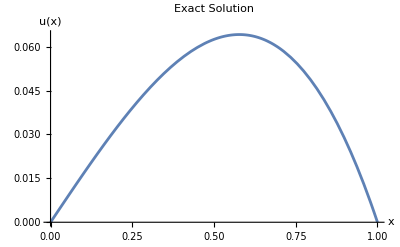

First Derivative: 0.166667 (1.-3. x^2)

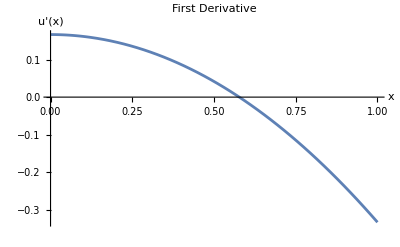

```mathematica
{Uexact, dUexact} = SolveExact[defineExact, g , True];
```

### Linear Elements

```mathematica
NumberElements = 4;
ExtremeElementsOrder = 3; (*First and last elements*)
InternalElementsOrder = 3;
SameSize = True; (*True => ElementSizes is ignored; False => Use ElementSizes *)
ElementSizes = {1}; (* Each element size will be divided by the total size*)
```

Approximation error: 3.04292×10^-13

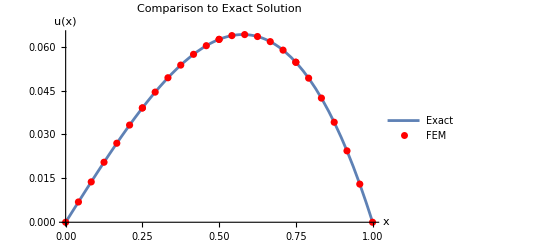

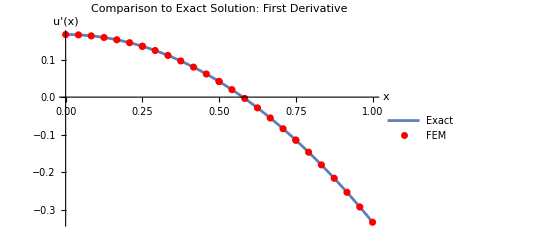

```mathematica
{Nodes, ElemNodes, ElemOrders,fRight} = preSolve1DFEM[defineExact, g, NumberElements, ExtremeElementsOrder, InternalElementsOrder, SameSize, ElementSizes];
{StiffMatrix,ForceVector, Solution,ApproxValues, dApproxValues,GError} = Solve1DFEM[fRight, Nodes,ElemNodes,ElemOrders,nPointsPerElem, Uexact, dUexact, nPointsErrorIntPerElem];
Print["Approximation error: ",GError];
CompareExact[Uexact, ApproxValues, dApproxValues]
```

```mathematica
StiffMatrix //MatrixForm
ForceVector //MatrixForm
Solution //MatrixForm
```

(1.×10^12 | -4. | 0 | 0 | 0
-4. | 8. | -4. | 0 | 0
0 | -4. | 8. | -4. | 0
0 | 0 | -4. | 8. | -4.
0 | 0 | 0 | -4. | 1.×10^12)

(0.0104167
0.0625
0.125
0.1875
0.114583)

(1.66667×10^-13
0.0390625
0.0625
0.0546875
3.33333×10^-13)

### Quadratic Elements

```mathematica
NumberElements = 4;
ExtremeElementsOrder = 2; (*First and last elements*)
InternalElementsOrder = 2;
SameSize = True; (*True => ElementSizes is ignored; False => Use ElementSizes *)
ElementSizes = {1}; (* Each element size will be divided by the total size*)
```

Approximation error: 0.00233097

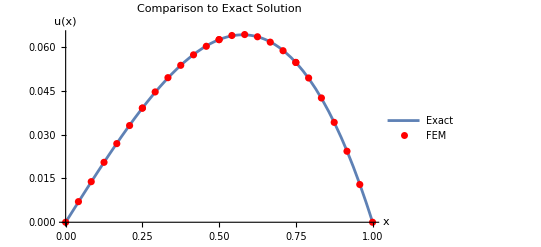

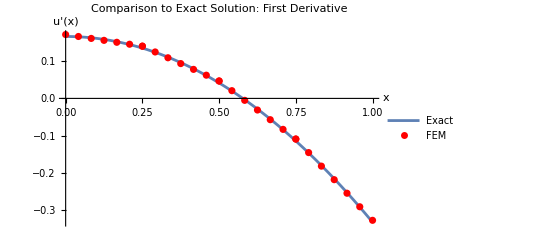

```mathematica
{Nodes, ElemNodes, ElemOrders,fRight} = preSolve1DFEM[defineExact, g, NumberElements, ExtremeElementsOrder, InternalElementsOrder, SameSize, ElementSizes];
{StiffMatrix,ForceVector,Solution,ApproxValues, dApproxValues,GError} = Solve1DFEM[fRight, Nodes,ElemNodes,ElemOrders,nPointsPerElem, Uexact, dUexact, nPointsErrorIntPerElem];
Print["Approximation error: ",GError];
CompareExact[Uexact, ApproxValues, dApproxValues]
```

### Error Function Analysis

```mathematica
NumberElementsMin = 4;
NumberElementsMax = 128;
```

Convergence exponent with elements of order 1: 0.999967

Convergence exponent with elements of order 2: 2.00001

Convergence exponent with elements of order 3: -0.00029547

Convergence exponent with elements of order 4: -0.00429215

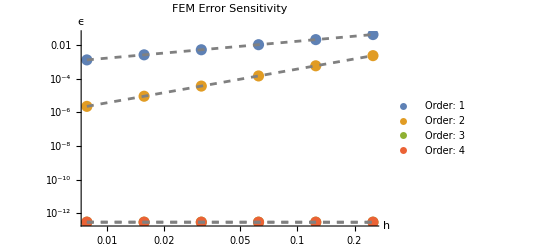

```mathematica
ErrorsStandard=FEMErrorAnalysis[Uexact, dUexact, defineExact, g,nPointsErrorIntPerElem,NumberElementsMin, NumberElementsMax,1, 4];
FEMErrorAnalysisPlot[ErrorsStandard,1]
```

## “Pulse” Problem

### “Right-side” Function

```mathematica
defineExact = True; (*True => g(x) == u(x); False => g(x) == -u'' + u == f(x) *)
eps = E^(-6);
g[x_]:= E^(-(x-1/2)^2/eps)-E^(-(1/2)^2/eps);
```

Exact Solution: (ⅇ^(-ⅇ^6 (x-1/2)^2)-1.57861×10^-44)(x)

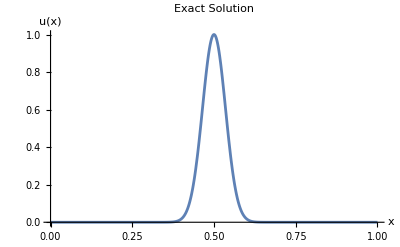

First Derivative: -2 ⅇ^(6-ⅇ^6 (x-1/2)^2) (x-1/2)

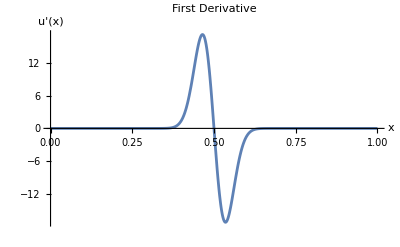

```mathematica
{Uexact, dUexact} = SolveExact[defineExact, g , True];
```

```mathematica
NumberElements = 20;
ExtremeElementsOrder = 2; (*First and last elements*)
InternalElementsOrder = 2;
SameSize = True; (*True => ElementSizes is ignored; False => Use ElementSizes *)
ElementSizes = {1}; (* Each element size will be divided by the total size*)
```

```mathematica
Off[LinearSolve::luc];
```

Approximation error: 0.827488

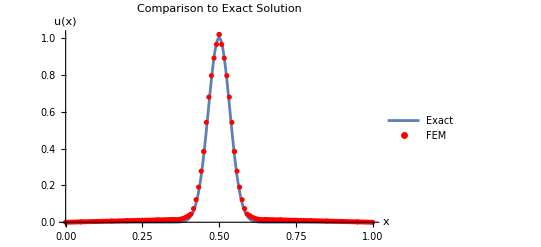

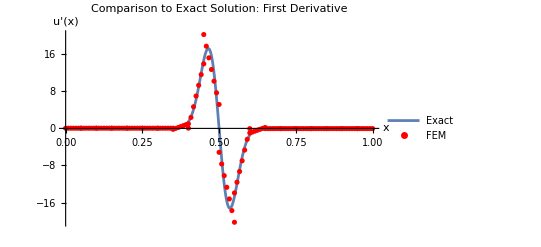

```mathematica
{Nodes, ElemNodes, ElemOrders,fRight} = preSolve1DFEM[defineExact, g, NumberElements, ExtremeElementsOrder, InternalElementsOrder, SameSize, ElementSizes];
{StiffMatrix,ForceVector,Solution,ApproxValues, dApproxValues,GError} = Solve1DFEM[fRight, Nodes,ElemNodes,ElemOrders,nPointsPerElem, Uexact, dUexact, nPointsErrorIntPerElem];
Print["Approximation error: ",GError];
CompareExact[Uexact, ApproxValues, dApproxValues]
```

Convergence exponent with elements of order 1: 0.973777

Convergence exponent with elements of order 2: 1.27407

Convergence exponent with elements of order 3: 0.199994

Convergence exponent with elements of order 4: 0.00400391

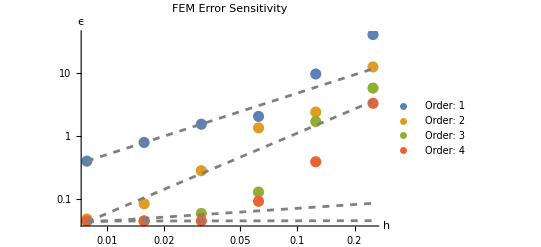

```mathematica
ErrorsStandard=FEMErrorAnalysis[Uexact, dUexact, defineExact, g,nPointsErrorIntPerElem,NumberElementsMin, NumberElementsMax,1, 4];
FEMErrorAnalysisPlot[ErrorsStandard,1]
```